```mathematica
α = 1/137
```

1/137

Скорость частицы S^+(m) в системе центра масс S^+S^--пары в зависимости от отношения m/M:

```mathematica
V[mRatio_] :=Sqrt[1 - 4 mRatio^2 ]
```

Скорость частицы S^+(m) относительно S^- в зависимости от отношения m/M:

```mathematica
Vrel[mRatio_] := V[mRatio]/(1 - 2 mRatio^2)
```

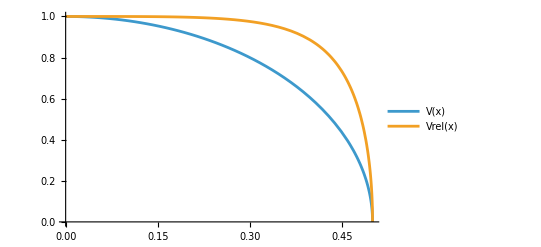

```mathematica
Plot[{V[x], Vrel[x]}, {x, 0. , 0.5}, PlotLegends->"Expressions"]
```

Фактор Гамова-Зоммерфельда-Сахарова:

```mathematica
GSS[v_] := (2 Pi α/v)/(1-Exp[-2 Pi α/v]);
```

Фактор Кратера-Алстина-Сазджана:

```mathematica
CAS[v_] := (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/v]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/v];
```

Фактор Фарри:

```mathematica
Furry[v_] := Exp[Pi α/v];
```

```mathematica
Plot[{Furry[V[x], Furry[Vrel[x]]]}, {x, 0., 0.5}]
```

-Graphics-

General::munfl: Exp[-4.58303×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.2648×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.1192×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

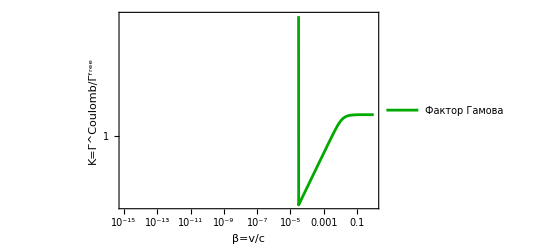

```mathematica
LogLogPlot[CAS[v]/ GSS[v], {v,10^-15,1},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана"}, Frame->True, AxesLabel->{HoldForm[β=HoldForm[v]/c],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]}]
```

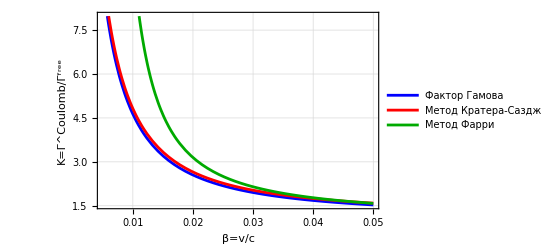

```mathematica
Plot[{GSS[v], 1.04 CAS[v], Furry[v]}, {v, 0.005,0.05},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[β=HoldForm[v]/c],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]}]
```

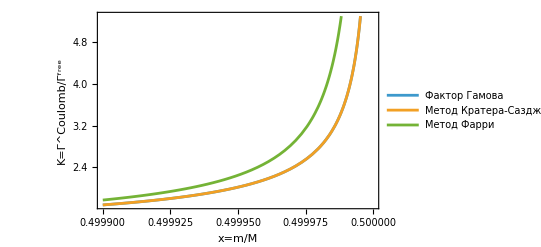

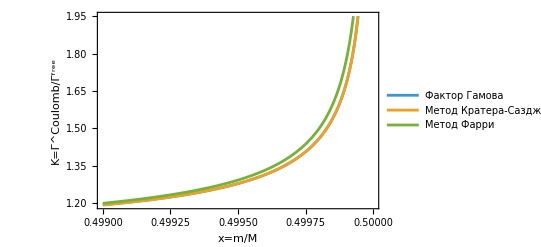

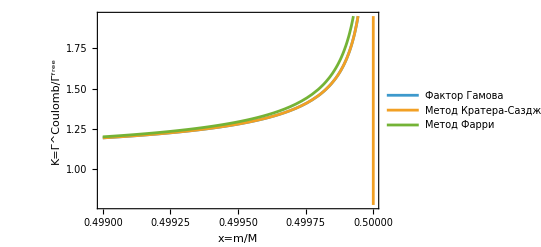

-Graphics-

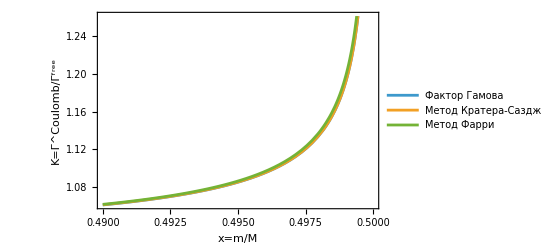

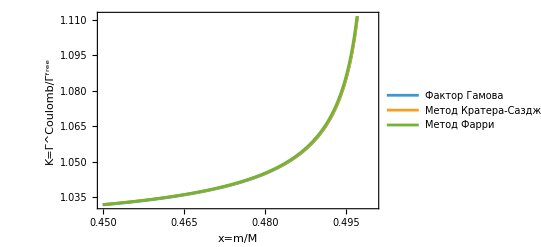

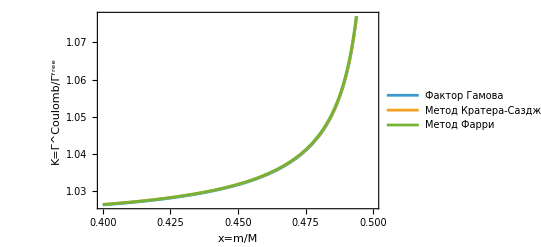

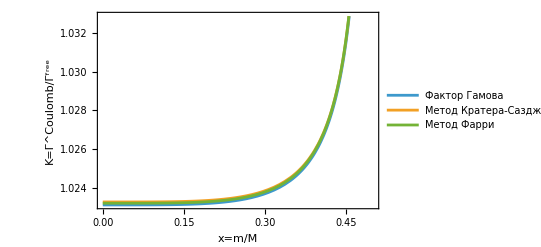

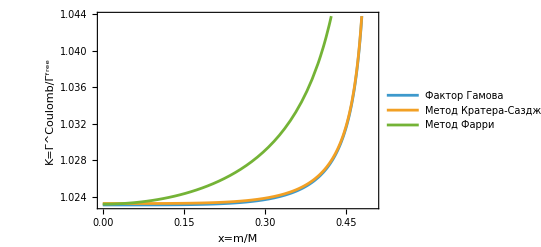

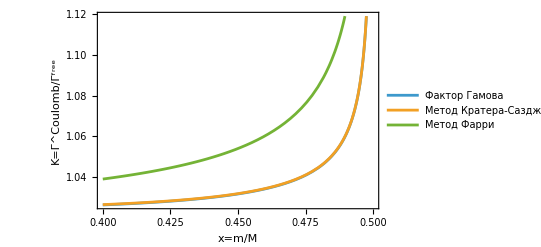

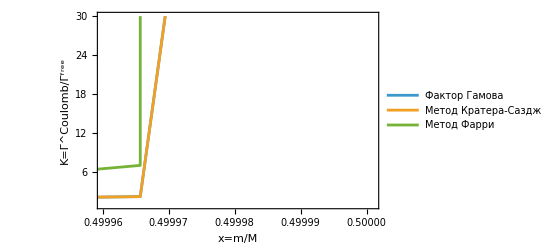

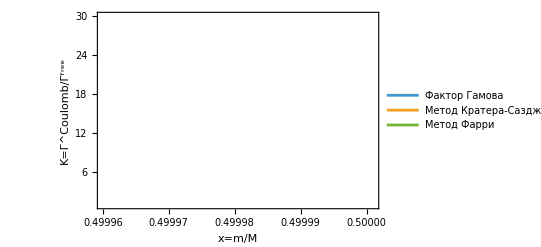

-Graphics-

-Graphics-

-Graphics-

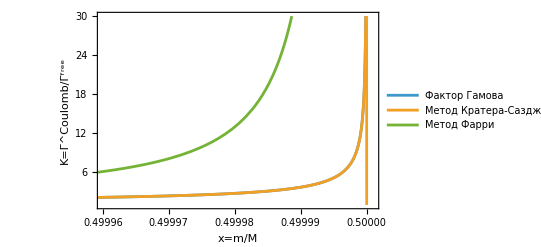

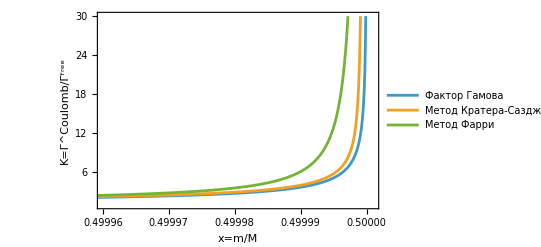

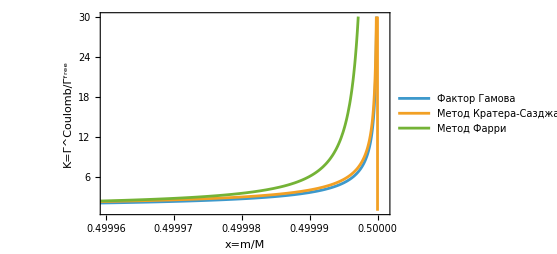

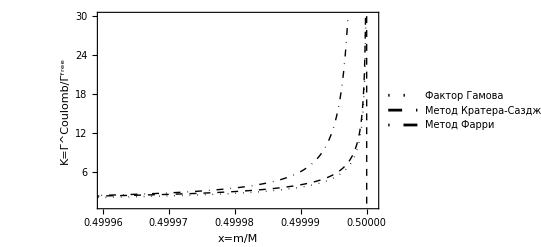

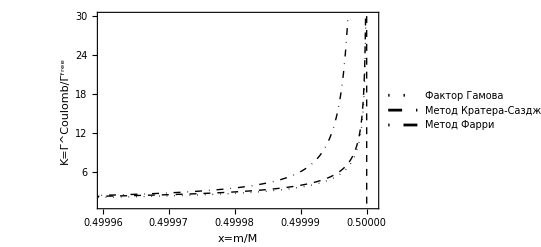

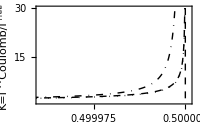

```mathematica
Plot[{GSS[Vrel[x]],  CAS[Vrel[x]], Furry[Vrel[x]]}, {x, 0.4999,0.4999999995},LabelStyle->{GrayLevel[0],Bold},PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]}]
```

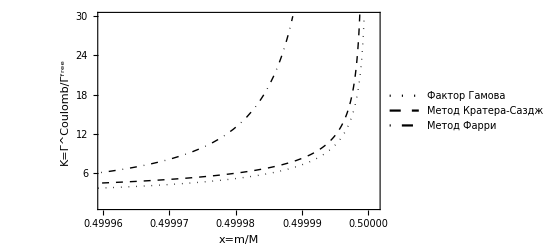

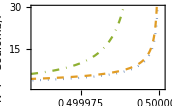

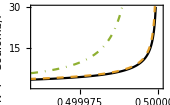

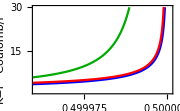

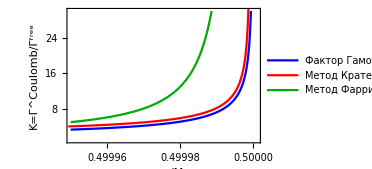

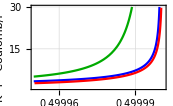

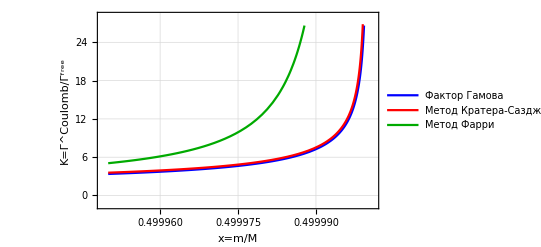

```mathematica
Plot[{(2 Pi α/Sqrt[1-4 (x/10000+0.5)^2])/(1-Exp[-2 Pi α/Sqrt[1-4 (x/10000+0.5)^2]]), (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/Sqrt[1-4 (x/10000+0.5)^2]]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/Sqrt[1-4 (x/10000+0.5)^2]], Exp[Pi α/Sqrt[1-4 (x/100000+0.5)^2]]}, {x, -10,0},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]},PlotRange-> {{-10,0.1},{1,30}}]
```

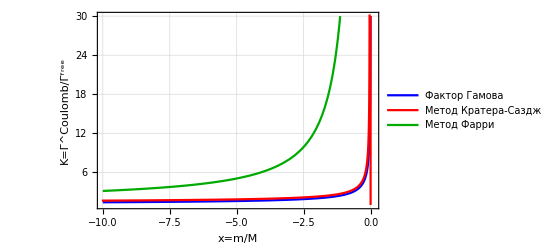

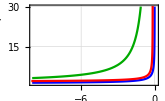

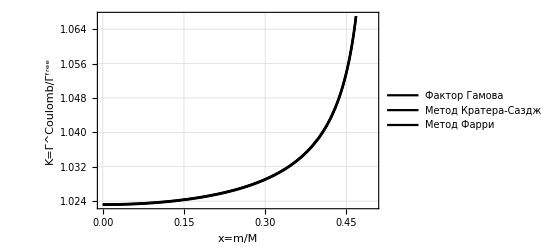

```mathematica
Plot[{(2 Pi α/Sqrt[1-4 x^2])/(1-Exp[-2 Pi α/Sqrt[1-4 x^2]]), (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/Sqrt[1-4 x^2]]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/Sqrt[1-4 x^2]], Exp[Pi α/Sqrt[1-4 x^2]]}, {x, 0,0.5},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Black,Black,Black}]
```